Last modified on: Tuesday, July 10, 2018 at 21:25

Author Info

Yash Akhauri

Sebastian Bodenstein

BITS Pilani

Poster Session Content

Introducing Hadamard Binary Neural Networks

1) Develop high performance kernels for HBNN operations.
2) Implement HBNN MLP in Wolfram Language, and inspect its performance on the MNIST dataset.
3) Study the high dimensional geometry of HBNNs.
4) Solve the scalability deadlock of InnerProduct.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

1) Faster convergence with respect to vanilla binarization techniques.
2) Consistently 10 times faster than CMMA algorithm. 
3) At par with MKL GEMM with minimal optimization.
4) Angle of randomly initialized vectors preserved in high dimensional spaces. (Approximately 37 degrees as vector length approach infinity.)
5) Histogram has greater granularity than Binary Neural Networks.

1) Conduct a study of the communication costs associated with this architecture.
2) Implement im2col convolution methods with low memory overhead.
3) Test accuracy on deep convolutional and language models.
4) Develop a distributed framework optimized for AI training.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

An analysis of Hadamard Binary Neural Networks

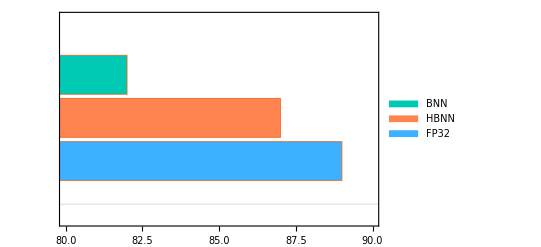
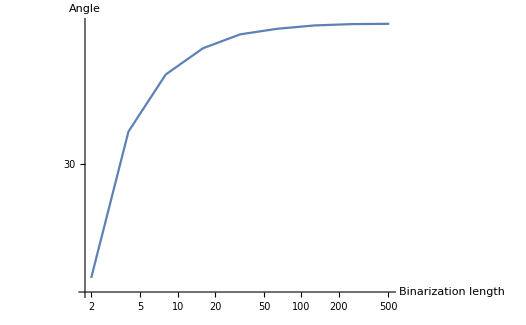
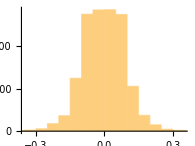
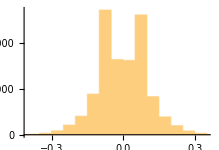
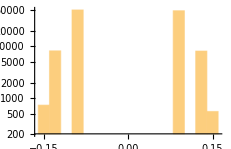
-Graphics-
Accuracy on MNIST
 -Graphics-
Performance analysis 
-Graphics--Graphics-
Angle Preservation property
-Graphics-
Weight histogram analysis
	      Full Precision	       Hadamard BNN	      	   	      	         BNN
-Graphics--Graphics--Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

Deep neural networks are an important tool in modern applications. It has become a major challenge to accelerate their training. As the complexity of our training tasks increase, the computation does too. For sustainable machine learning at scale, we need distributed systems that can leverage the available hardware effectively. This research hopes to exceed the current state of the art performance of neural networks by introducing a new architecture optimized for distributability. The scope of this work is not just limited to optimizing neural network training for large servers, but also to bring training to heterogeneous environments; paving way for a distributed peer to peer mesh computing platform that can harness the wasted resources of idle computers in a workplace for AI.
  
  Advantages of Hadamard Binarization
1. Faster convergence with respect to vanilla binarization techniques.
  2. Consistently about 10 times faster than CMMA algorithm.
  3. Angle of randomly initialized vectors preserved in high dimensional spaces. (Approximately 37 degrees as vector length approach infinity.)
4. Reduced communication times for distributed deep learning.
  5. Optimization of im2col algorithm for faster inference.
  6. Reduction of model sizes.
  
  The HBNN model gives 87 % accuracy, whereas the BNN model (Binary Neural Networks) give only 82 %. These networks have only been trained for 5 epochs.
  Hadamard BNN preserves the distribution of the weights much better.
  Binarization approximately preserves the direction of high dimensional vectors. The figure above demonstrates that the angle between a random vector (from a standard normal distribution) and its binarized version converges to ~ 37 degrees as the dimension of the vector goes to infinity. This angle is exceedingly small in high dimensions.

#### Code

GitHub links:

https://github.com/akhauriyash/Summer2018Starter

https://github.com/akhauriyash/Hadamard-Nets

#### Conclusions in Detail

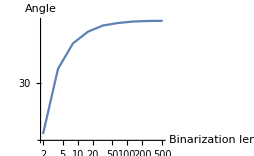
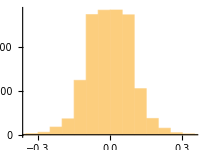
#### All Visualizations -Graphics- -Graphics- -Graphics--Graphics- -Graphics- -Graphics--Graphics--Graphics-